```mathematica
ClearAll["Global`*"]
```

```mathematica
t2[r_, t_, i_, s_]:=(i-1)/(2s)t+(s-1)/(2i)r+r/(2i*s)*t;
t1[r_, t_, i_, s_]:=-2 √(r*t*(2i-r)*(2s-t));
EAM[r_, t_, i_, s_]:=t1[r, t, i, s]+t2[r, t, i ,s];
```

### Contour Plots for EAM

```mathematica
tmax=10;
rmax =10;
```

```mathematica
cp[f_,rmax_, tmax_]:=ContourPlot[f[r, t],{r,0,rmax},{t,0,tmax} , Contours->15, FrameStyle->Directive[Black, Thick], FrameLabel->{"r","t"},LabelStyle->{18, Black, FontFamily->"Helvetica"} ,ClippingStyle->Automatic, PlotRange->{{0,rmax},{0,tmax}}, ContourShading->Automatic,PlotLegends->BarLegend[Automatic,6]];
shower[f_,p_,minp_]:=Show[cp[f,2p[[1]],2p[[2]]], Graphics[{PointSize[Large],Red,Point[minp]}],Graphics[Inset[Framed[Style[StringTemplate["I=`` ; S=``"][p[[1]],p[[2]]],Bold,18,White,FontFamily->"Times New Roman"],BaseStyle->{White, 24}],Scaled[{0.3,0.85}]]]];
```

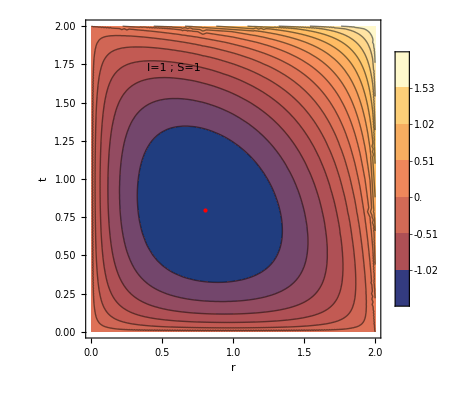

contour0.png

```mathematica
p0={1,1};
min0={0.8 ,0.8};
f0[r_,t_]:=EAM[r, t,p0[[1]],p0[[2]]];
shower[f0, p0,min0]
Export["contour0.png",shower[f0, p0,min0], ImageResolution->1200]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["contour1.pdf"]]]
```

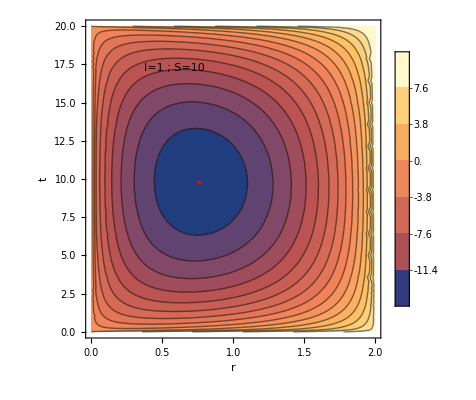

contour1.png

```mathematica
p1={1,10};
min1={0.757867, 9.80476};
f1[r_,t_]:=EAM[r, t,p1[[1]],p1[[2]]];
shower[f1, p1,min1]
Export["contour1.png",shower[f1, p1,min1], ImageResolution->1200]
```

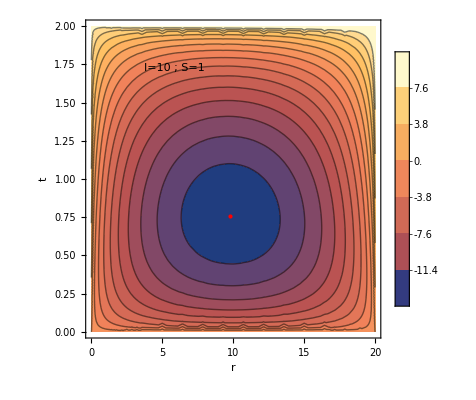

contour2.png

```mathematica
p2={10,1};
min2={9.80476 ,0.757867};
f2[r_,t_]:=EAM[r, t,p2[[1]],p2[[2]]];
shower[f2, p2,min2]
Export["contour2.png",shower[f2, p2,min2], ImageResolution->1200]
```

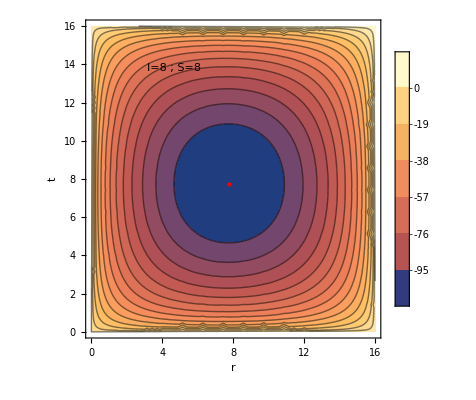

contour3.png

```mathematica
p3={8,8};
min3={7.750972762645929 ,7.750972762645929};
f3[r_,t_]:=EAM[r, t, p3[[1]],p3[[2]]];
shower[f3, p3,min3]
Export["contour3.png",shower[f3, p3,min3], ImageResolution->1200]
```

### Minima points for EAM